# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Brazil","Czech Republic","Chile"};
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/omicron-countries_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-11

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-11

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{Australia,Brazil,Canada,Chile,Czech Republic,Denmark,France,Germany,India,Ireland,Israel,Netherlands,Norway,Singapore,South Africa,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{Australia,Canada,Denmark,France,Germany,India,Ireland,Israel,Netherlands,Norway,Singapore,South Africa,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.005];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

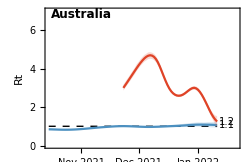
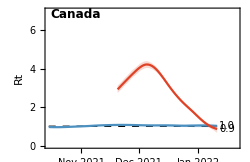
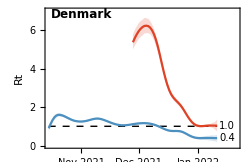
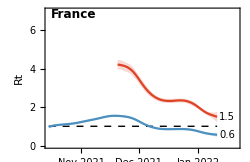
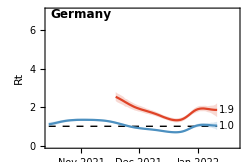
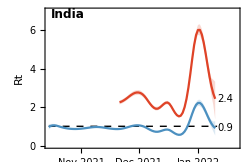
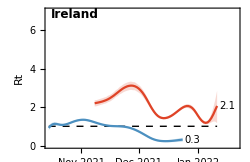
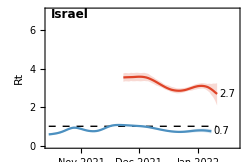
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-01-11,1.2,0.9,1.5},Canada→{2022-01-11,0.9,0.7,1.},Denmark→{2022-01-11,1.,0.7,1.4},France→{2022-01-11,1.5,1.2,1.8},Germany→{2022-01-11,1.9,1.5,2.2},India→{2022-01-10,2.4,1.4,3.3},Ireland→{2022-01-11,2.1,1.2,2.8},Israel→{2022-01-11,2.7,2.1,3.2},Netherlands→{2022-01-11,1.6,1.4,1.9},Norway→{2022-01-11,1.1,0.7,1.4},Singapore→{2022-01-11,0.8,0.5,1.},South Africa→{2022-01-11,0.8,0.5,1.},Spain→{2022-01-11,0.7,0.4,0.9},Sweden→{2022-01-11,1.2,0.8,1.5},Switzerland→{2022-01-11,1.2,1.,1.4},Thailand→{2022-01-11,1.8,1.4,2.2},United Kingdom→{2022-01-11,0.6,0.4,0.8},USA→{2022-01-11,1.1,0.7,1.4}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/omicron-countries_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.005];
```

```mathematica
rData=DeleteCases[rData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.35}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,14]},
{-0.35,0.35}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

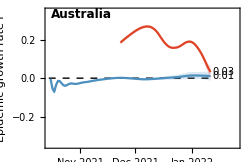
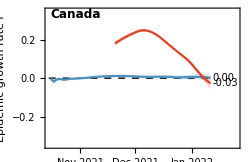
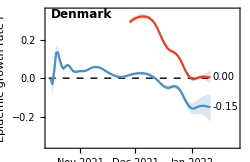
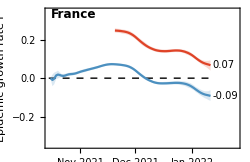
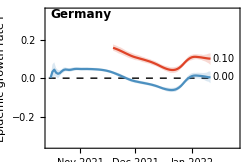
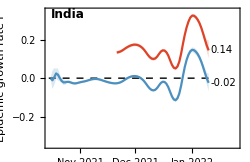
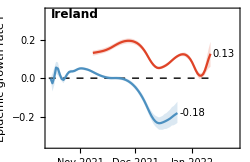
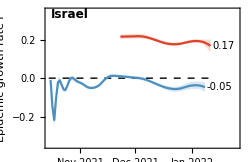
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-01-11,0.03,0.,0.06},Canada→{2022-01-11,-0.03,-0.06,0.01},Denmark→{2022-01-11,0.,-0.03,0.04},France→{2022-01-11,0.07,0.04,0.09},Germany→{2022-01-11,0.1,0.07,0.13},India→{2022-01-10,0.14,0.1,0.2},Ireland→{2022-01-11,0.13,0.06,0.19},Israel→{2022-01-11,0.17,0.14,0.2},Netherlands→{2022-01-11,0.08,0.06,0.11},Norway→{2022-01-11,0.01,-0.03,0.04},Singapore→{2022-01-11,-0.06,-0.11,0.},South Africa→{2022-01-11,-0.05,-0.08,0.},Spain→{2022-01-11,-0.07,-0.13,-0.02},Sweden→{2022-01-11,0.02,-0.03,0.07},Switzerland→{2022-01-11,0.03,0.01,0.06},Thailand→{2022-01-11,0.1,0.08,0.14},United Kingdom→{2022-01-11,-0.08,-0.11,-0.06},USA→{2022-01-11,0.02,-0.03,0.05}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,countries]
```

{Australia→{2022-01-11,21.7,10.9,-402.2},Canada→{2022-01-11,-26.3,127.4,-12.},Denmark→{2022-01-11,176.5,16.5,-20.9},France→{2022-01-11,10.3,7.5,17.6},Germany→{2022-01-11,6.8,5.4,10.1},India→{2022-01-10,4.8,3.5,6.7},Ireland→{2022-01-11,5.5,3.7,11.8},Israel→{2022-01-11,4.1,3.4,5.1},Netherlands→{2022-01-11,8.6,6.4,12.3},Norway→{2022-01-11,111.8,15.7,-20.1},Singapore→{2022-01-11,-11.9,139.3,-6.4},South Africa→{2022-01-11,-15.3,-276.9,-8.5},Spain→{2022-01-11,-9.6,-37.6,-5.4},Sweden→{2022-01-11,35.1,10.1,-24.3},Switzerland→{2022-01-11,20.8,11.1,117.2},Thailand→{2022-01-11,6.6,5.1,9.1},United Kingdom→{2022-01-11,-8.4,-12.2,-6.1},USA→{2022-01-11,39.8,13.3,-24.9}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/omicron-countries_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{60,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{50,1000000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

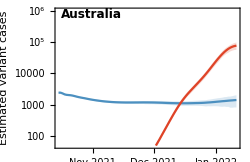
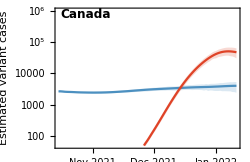
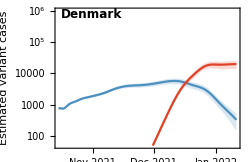
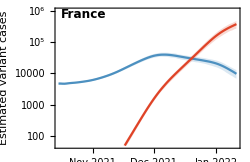
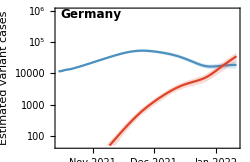
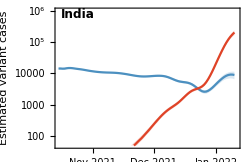
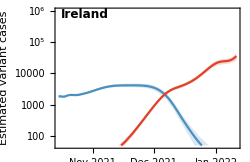
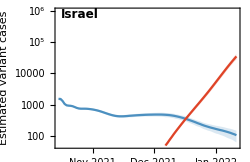
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

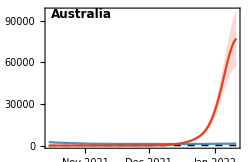
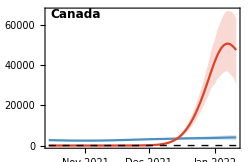
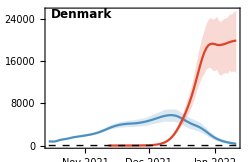
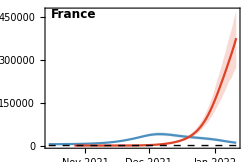
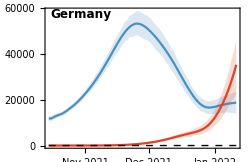
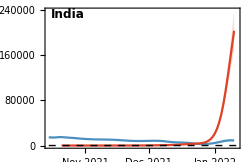
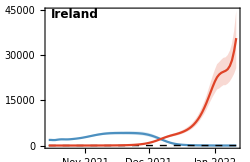
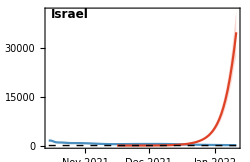
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,countries]
```

{Australia→{2022-01-11,77299,56391,97216},Canada→{2022-01-11,47604,30363,63003},Denmark→{2022-01-11,19915,13706,25549},France→{2022-01-11,375467,271950,471098},Germany→{2022-01-11,35344,22753,46279},India→{2022-01-10,203261,168249,238620},Ireland→{2022-01-11,35701,25720,44775},Israel→{2022-01-11,34935,27554,41566},Netherlands→{2022-01-11,27651,24402,30966},Norway→{2022-01-11,6187,3956,8132},Singapore→{2022-01-11,844,649,1053},South Africa→{2022-01-11,5631,4544,6517},Spain→{2022-01-11,183145,137285,235399},Sweden→{2022-01-11,46447,36626,56487},Switzerland→{2022-01-11,40651,31904,49162},Thailand→{2022-01-11,8752,7681,9706},United Kingdom→{2022-01-11,97351,70858,121777},USA→{2022-01-11,793957,592256,992607}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,countries];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

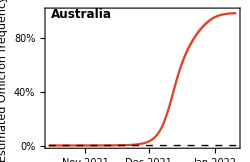
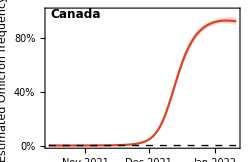
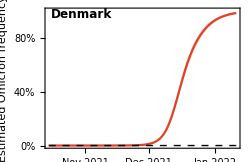
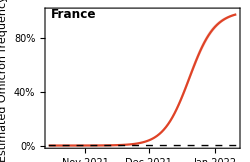
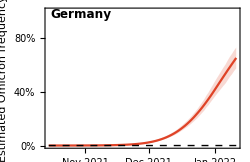
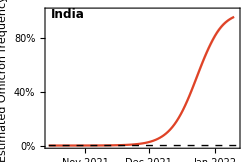
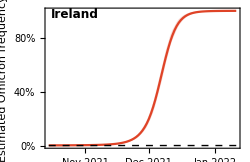
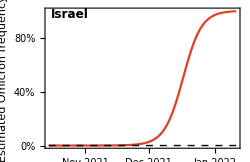
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[panels,4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,countries]
```

{Australia→{2022-01-11,0.98,0.97,0.99},Canada→{2022-01-11,0.92,0.89,0.95},Denmark→{2022-01-11,0.98,0.98,0.99},France→{2022-01-11,0.97,0.97,0.98},Germany→{2022-01-11,0.65,0.57,0.73},India→{2022-01-10,0.95,0.95,0.96},Ireland→{2022-01-11,1.,1.,1.},Israel→{2022-01-11,1.,1.,1.},Netherlands→{2022-01-11,0.89,0.88,0.91},Norway→{2022-01-11,0.9,0.86,0.93},Singapore→{2022-01-11,0.95,0.94,0.97},South Africa→{2022-01-11,1.,1.,1.},Spain→{2022-01-11,0.98,0.98,0.99},Sweden→{2022-01-11,0.97,0.96,0.98},Switzerland→{2022-01-11,0.97,0.96,0.97},Thailand→{2022-01-11,0.98,0.98,0.99},United Kingdom→{2022-01-11,0.99,0.99,0.99},USA→{2022-01-11,0.92,0.87,0.97}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[country_,variant_]:=Module[{popSize},
popSize=QuantityMagnitude[CountryData[country,"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[country,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.25,0.4}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,countries];
```

```mathematica
legendPanel=PointLegend[{colors[[3]]},{variants[[3]]},LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

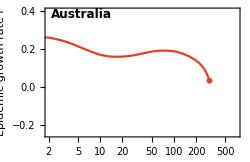
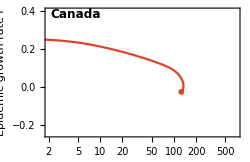
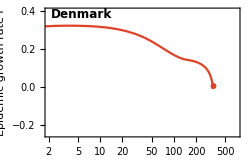
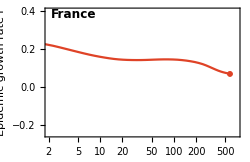
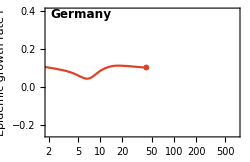
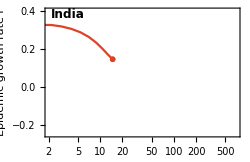
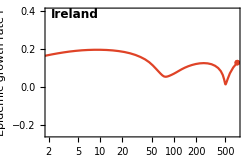
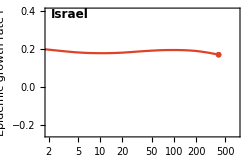
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_variant-cases-vs-rt.png

```mathematica
countryLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,countries];
```

```mathematica
figLines=ListLogLinearPlot[countryLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,700},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
countryPoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,countries];
```

```mathematica
figPoints=ListLogLinearPlot[countryPoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,700},
{-0.1,0.35}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

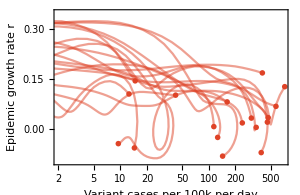

```mathematica
fig=Show[figLines,figPoints]
```

## Comparison to vaccination rate

Country-level vaccination data is obtained from Our World in Data, following instructions at https://github.com/owid/covid-19-data/blob/master/public/data/README.md

The full CSV is available at: https://covid.ourworldindata.org/data/owid-covid-data.csv

```mathematica
comparisonDate=DateString[DatePlus[endDate,-3],{"Year","-","Month", "-","Day"}]
```

2022-01-08

### Data

```mathematica
vData=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv","CSV"];
```

```mathematica
Dimensions[vData]
```

{153873,67}

```mathematica
header=First[vData]
```

{iso_code,continent,location,date,total_cases,new_cases,new_cases_smoothed,total_deaths,new_deaths,new_deaths_smoothed,total_cases_per_million,new_cases_per_million,new_cases_smoothed_per_million,total_deaths_per_million,new_deaths_per_million,new_deaths_smoothed_per_million,reproduction_rate,icu_patients,icu_patients_per_million,hosp_patients,hosp_patients_per_million,weekly_icu_admissions,weekly_icu_admissions_per_million,weekly_hosp_admissions,weekly_hosp_admissions_per_million,new_tests,total_tests,total_tests_per_thousand,new_tests_per_thousand,new_tests_smoothed,new_tests_smoothed_per_thousand,positive_rate,tests_per_case,tests_units,total_vaccinations,people_vaccinated,people_fully_vaccinated,total_boosters,new_vaccinations,new_vaccinations_smoothed,total_vaccinations_per_hundred,people_vaccinated_per_hundred,people_fully_vaccinated_per_hundred,total_boosters_per_hundred,new_vaccinations_smoothed_per_million,new_people_vaccinated_smoothed,new_people_vaccinated_smoothed_per_hundred,stringency_index,population,population_density,median_age,aged_65_older,aged_70_older,gdp_per_capita,extreme_poverty,cardiovasc_death_rate,diabetes_prevalence,female_smokers,male_smokers,handwashing_facilities,hospital_beds_per_thousand,life_expectancy,human_development_index,excess_mortality_cumulative_absolute,excess_mortality_cumulative,excess_mortality,excess_mortality_cumulative_per_million}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{iso_code→1,continent→2,location→3,date→4,total_cases→5,new_cases→6,new_cases_smoothed→7,total_deaths→8,new_deaths→9,new_deaths_smoothed→10,total_cases_per_million→11,new_cases_per_million→12,new_cases_smoothed_per_million→13,total_deaths_per_million→14,new_deaths_per_million→15,new_deaths_smoothed_per_million→16,reproduction_rate→17,icu_patients→18,icu_patients_per_million→19,hosp_patients→20,hosp_patients_per_million→21,weekly_icu_admissions→22,weekly_icu_admissions_per_million→23,weekly_hosp_admissions→24,weekly_hosp_admissions_per_million→25,new_tests→26,total_tests→27,total_tests_per_thousand→28,new_tests_per_thousand→29,new_tests_smoothed→30,new_tests_smoothed_per_thousand→31,positive_rate→32,tests_per_case→33,tests_units→34,total_vaccinations→35,people_vaccinated→36,people_fully_vaccinated→37,total_boosters→38,new_vaccinations→39,new_vaccinations_smoothed→40,total_vaccinations_per_hundred→41,people_vaccinated_per_hundred→42,people_fully_vaccinated_per_hundred→43,total_boosters_per_hundred→44,new_vaccinations_smoothed_per_million→45,new_people_vaccinated_smoothed→46,new_people_vaccinated_smoothed_per_hundred→47,stringency_index→48,population→49,population_density→50,median_age→51,aged_65_older→52,aged_70_older→53,gdp_per_capita→54,extreme_poverty→55,cardiovasc_death_rate→56,diabetes_prevalence→57,female_smokers→58,male_smokers→59,handwashing_facilities→60,hospital_beds_per_thousand→61,life_expectancy→62,human_development_index→63,excess_mortality_cumulative_absolute→64,excess_mortality_cumulative→65,excess_mortality→66,excess_mortality_cumulative_per_million→67}

```mathematica
vData=Drop[vData,1];
```

```mathematica
Length[vData]
```

153872

Replace “United States” with “USA”

```mathematica
vData=Map[Join[#[[1;;2]],{If[#[[3]]=="United States","USA",#[[3]]]},#[[4;;-1]]]&,vData];
```

Remove lines lacking data

```mathematica
vData=DeleteCases[vData,x_/;x[[43]]==""];
```

```mathematica
vData=DeleteCases[vData,x_/;x[[44]]==""];
```

```mathematica
fullyVacGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,43]],Null]
]
```

```mathematica
fullyVacGather["United Kingdom"]
```

69.92

```mathematica
fullyVacGather["Netherlands"]
```

71.38

```mathematica
boosterGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,series[[1,44]],Null]
]
```

```mathematica
boosterGather["United Kingdom"]
```

52.08

```mathematica
totalCasesGather[country_]:=Module[{series},
series=Cases[vData,x_/;x[[3]]==country&&x[[4]]==comparisonDate];
If[Length[series]>0,100*series[[1,11]]/1000000,Null]
]
```

```mathematica
totalCasesGather["USA"]
```

17.9528

```mathematica
series=DeleteCases[Table[{country,fullyVacGather[country],boosterGather[country],totalCasesGather[country],FirstCase[rGather[country,"Omicron"],x_/;x[[1]]==comparisonDate][[2]]},{country,countries}],x_/;x[[2]]==Null||x[[3]]==Null||x[[4]]==Null]
```

{{Australia,77.15,13.83,3.77094,0.0892081},{Canada,77.54,25.47,6.58567,-0.00486422},{Denmark,80.04,53.66,16.3459,0.00791025},{France,74.43,38.45,17.5932,0.0761995},{Germany,71.26,42.54,8.97719,0.104578},{Ireland,77.2,48.06,19.2,0.0412755},{Israel,64.2,49.09,15.9896,0.184075},{Netherlands,71.38,32.43,19.3155,0.100393},{Norway,72.07,34.63,8.05368,0.0623069},{Singapore,86.61,45.86,5.22228,0.0668578},{Switzerland,67.21,29.64,17.0181,0.0534763},{United Kingdom,69.92,52.08,21.0626,-0.0571208},{USA,62.13,22.91,17.9528,0.047678}}

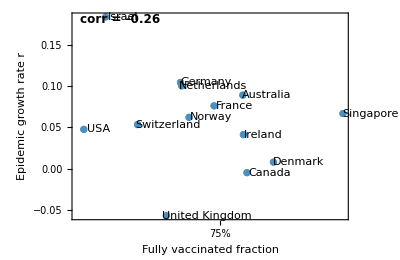

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{2,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,2]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

```mathematica
Export["figures/"<>dataset<>"_r-vs-vaccinated-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-vaccinated-fraction.png

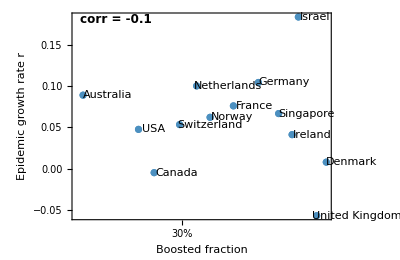

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{3,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Boosted fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,10}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,3]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

```mathematica
Export["figures/"<>dataset<>"_r-vs-boosted-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-boosted-fraction.png

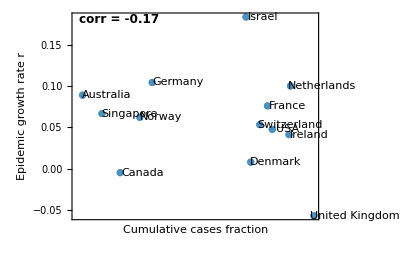

```mathematica
fig=ListPlot[Map[{#}&,series[[All,{4,5}]]],PlotLabels->Placed[series[[All,1]],Right],PlotStyle->colors[[2]],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Cumulative cases fraction","Epidemic growth rate r"},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[i]<>"%"},{i,0,100,5}],Automatic}},PlotRangePadding->{{Scaled[0.02],Scaled[0.18]},{Scaled[0.03],Scaled[0.05]}},AspectRatio->0.65,Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[series[[All,4]],series[[All,5]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

```mathematica
Export["figures/"<>dataset<>"_r-vs-infected-fraction.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_r-vs-infected-fraction.png